```mathematica
a=Table[α,{i,3}];
m={1,1,1,1};
Subscript[μ, i][i_]:=1/m[[4]] (m[[Mod[i+1,3,1]]] m[[Mod[i+2,3,1]]])/(m[[Mod[i+1,3,1]]]+m[[Mod[i+2,3,1]]]);
Subscript[μ, jk][i_]:=1/m[[4]] (m[[i]] (m[[Mod[i+1,3,1]]]+m[[Mod[i+2,3,1]]]))/(m[[i]]+m[[Mod[i+1,3,1]]]+m[[Mod[i+2,3,1]]]);
Subscript[ϕ, jk][i_]:=ArcTan[√((m[[i]] (Total[m[[;;-2]]]))/(m[[Mod[i+1,3,1]]] m[[Mod[i+2,3,1]]]))];
Mii[ν_,ρ_]:=Table[ν Cos[ν π/2]+Sin[ν π/2] ρ/(√(Subscript[μ, i][ii]) a[[ii]]),{ii,3}];
Mij[ν_]:=Table[If[ii≠jj,2 Sin[ν (Subscript[ϕ, jk][6-ii-jj]-π/2)]/Sin[2 Subscript[ϕ, jk][6-ii-jj]],0],{ii,3},{jj,3}];
M[ν_,ρ_]:=Mij[ν]+DiagonalMatrix[Mii[ν,ρ]];
M[ν,ρ]//MatrixForm
Simplify[Det[M[ν,ρ]]]
nu[ρ_]:=Solve[Det[M[ν,ρ]]==0,ν];
```

(ν Cos[(π ν)/2]+(√2 ρ Sin[(π ν)/2])/α | -(4 Sin[(π ν)/6])/(√3) | -(4 Sin[(π ν)/6])/(√3)
-(4 Sin[(π ν)/6])/(√3) | ν Cos[(π ν)/2]+(√2 ρ Sin[(π ν)/2])/α | -(4 Sin[(π ν)/6])/(√3)
-(4 Sin[(π ν)/6])/(√3) | -(4 Sin[(π ν)/6])/(√3) | ν Cos[(π ν)/2]+(√2 ρ Sin[(π ν)/2])/α)

ν^3 Cos[(π ν)/2]^3-16 ν Cos[(π ν)/2] Sin[(π ν)/6]^2-(128 Sin[(π ν)/6]^3)/(3 √3)+(3 √2 ν^2 ρ Cos[(π ν)/2]^2 Sin[(π ν)/2])/α-(16 √2 ρ Sin[(π ν)/6]^2 Sin[(π ν)/2])/α+(ρ^2 Sin[(π ν)/2] (2 √2 ρ Sin[(π ν)/2]^2+3 α ν Sin[π ν]))/α^3

```mathematica
nu[4]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[ν^3 Cos[(π ν)/2]^3-16 ν Cos[(π ν)/2] Sin[(π ν)/6]^2-(128 Sin[(π ν)/6]^3)/(3 √3)+12 √2 ν^2 Cos[(π ν)/2]^2 Sin[(π ν)/2]-64 √2 Sin[(π ν)/6]^2 Sin[(π ν)/2]+96 ν Cos[(π ν)/2] Sin[(π ν)/2]^2+128 √2 Sin[(π ν)/2]^3==0,ν]

```mathematica
Det[M[nuev[[1]],2]]
```

-2.60887×10^-23

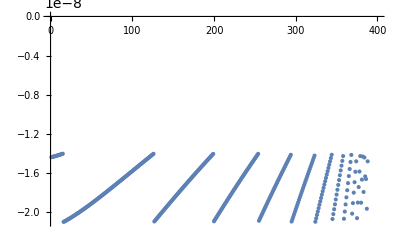

```mathematica
nuev=Table[ν/.nu[rho],{rho,0.001,4,0.01}];
ListPlot[nuev]
```

```mathematica
Mid[ν_,ρ_]:=Table[If[ii==jj,ν Cos[3 α]+Sin[3 α] (√2 ρ)/aa,-4/(√3) Sin[α]],{ii,3},{jj,3}]
```

```mathematica
Mid[ν,ρ]//MatrixForm
Simplify[Det[Mid[ν,ρ]]==0]
```

(ν Cos[3 α]+(√2 ρ Sin[3 α])/aa | -(4 Sin[α])/(√3) | -(4 Sin[α])/(√3)
-(4 Sin[α])/(√3) | ν Cos[3 α]+(√2 ρ Sin[3 α])/aa | -(4 Sin[α])/(√3)
-(4 Sin[α])/(√3) | -(4 Sin[α])/(√3) | ν Cos[3 α]+(√2 ρ Sin[3 α])/aa)

ν^3 Cos[3 α]^3+(3 √2 ν^2 ρ Cos[3 α]^2 Sin[3 α])/aa+(2 ρ^2 Sin[3 α]^2 (3 aa ν Cos[3 α]+√2 ρ Sin[3 α]))/aa^3==(16 Sin[α]^2 (9 aa ν Cos[3 α]+8 √3 aa Sin[α]+9 √2 ρ Sin[3 α]))/(9 aa)

```mathematica
s0=ν/.FindRoot[ν Cos[ν π/2]-8/(√3) Sin[ν π/6],{ν,1.001 I}]
rat=Exp[2 π/Abs[s0]]
√rat
```

0.+1.00624 ⅈ

515.035

22.6944